```mathematica
Multiway Minkowski Music Space
```

Minkowski Multiway Music

```mathematica
s1  = Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-01.wav"]
s2 = Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-02.wav"]
s3= Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-03.wav"]
s4 = Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-04.wav"]
s5 = Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-05.wav"]
s6 = Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-06.wav"]
s7 = Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-07.wav"]
s8= Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-08.wav"]
s9 = Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-09.wav"]
s10 = Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-10.wav"]

(*s2 :=emitSound@

Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-02.wav","Sound"]
s3 :=EmitSound@Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-03.wav","Sound"]
s4 :=EmitSound@Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-04.wav","Sound"]
s5 :=EmitSound@Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-05.wav","Sound"]
s6 :=EmitSound@Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-06.wav","Sound"]
s7 :=EmitSound@Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-07.wav","Sound"]
s8 :=EmitSound@Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-08.wav","Sound"]
s9 :=EmitSound@Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-09.wav","Sound"]
s10 :=EmitSound@Import["C:\\Users\\jdiet\\OneDrive\\Documents\\GitHub\\metalambda\\rulial-music\\handpan-samples\\hp-10.wav","Sound"]*)
```

```mathematica
AudioPlot[AudioData[s1]]
```

AudioData::audio: Expecting an audio object instead of Null.

AudioPlot::audio: Expecting an audio object instead of AudioData[Null].

AudioPlot[AudioData[Null]]

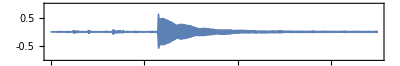
```mathematica
-Graphics-
ListLinePlot[AudioData[s1][[1]]]
```

-Graphics-

AudioData::audio: Expecting an audio object instead of Null.

ListLinePlot::lpn: Null is not a list of numbers or pairs of numbers.

ListLinePlot[Null]

-Graphics-

-Graphics-

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

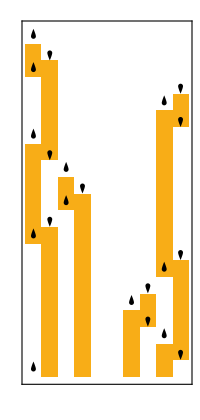

```mathematica
-Graphics-

(*instruments={"Harpsichord","Marimba","Sitar","Flute"};

sounds=Sound[SoundNote[{"C","G"},1,#]]&/@instruments*)

sounds2 = List[s1, s2, s3, s4, s5, s6, s7, s8, s9, s10]

RulePlot[TuringMachine[2506],{1,{0,0,0,0,0,0,0,0,0,0}},20]
```

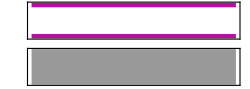
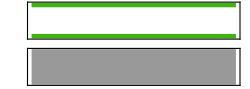
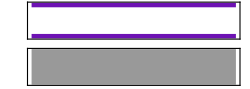
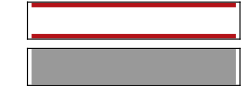
```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}


AudioJoin@@(AudioOverlay@Pick[sounds2,#,1]&/@Rest@TuringMachine[2506,{1,{0,0,0,0,0,0,0,0,0,0}},20][[All,2]])

AudioJoin@@(AudioOverlay@Pick[sounds2,#,1]&/@Rest@TuringMachine[2506,{1,{0,1,0,1,0,1,0,1,0,1}},20][[All,2]])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

AudioOverlay::audiolist: The specified argument {Null} should be a vector of audio objects or a vector or {audio, offset} pairs.

AudioOverlay::audiolist: The specified argument {Null,Null} should be a vector of audio objects or a vector or {audio, offset} pairs.

AudioOverlay::audiolist: The specified argument {Null} should be a vector of audio objects or a vector or {audio, offset} pairs.

General::stop: Further output of AudioOverlay::audiolist will be suppressed during this calculation.

AudioJoin::audiolistpos: An audio object or a vector of {audio, offset} is expected at position 1.

AudioJoin[AudioOverlay[{Null}],AudioOverlay[{Null,Null}],AudioOverlay[{Null}],AudioOverlay[{Null,Null}],AudioOverlay[{Null,Null,Null}],AudioOverlay[{Null,Null}],AudioOverlay[{Null,Null,Null}],AudioOverlay[{Null,Null}],AudioOverlay[{Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}]]

AudioOverlay::audiolist: The specified argument {Null,Null,Null,Null,Null,Null} should be a vector of audio objects or a vector or {audio, offset} pairs.

AudioOverlay::audiolist: The specified argument {Null,Null,Null,Null,Null} should be a vector of audio objects or a vector or {audio, offset} pairs.

AudioOverlay::audiolist: The specified argument {Null,Null,Null,Null,Null,Null} should be a vector of audio objects or a vector or {audio, offset} pairs.

General::stop: Further output of AudioOverlay::audiolist will be suppressed during this calculation.

AudioJoin::audiolistpos: An audio object or a vector of {audio, offset} is expected at position 1.

AudioJoin[AudioOverlay[{Null,Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null}],AudioOverlay[{Null,Null,Null,Null,Null}]]

```mathematica
(*Calculated distance from observer 1  and time to receive*)
```